```mathematica
rawData = Drop[Import["Desktop/VEIC homework/VEIC_master_2.csv"],4];
```

```mathematica
Total[rawData[[All,8]]]*.25
```

1.64131×10^6

```mathematica
coastLineArray={{"Alaska", 54563,1477950},{"Florida",13576,138888},{"California",5515,403466},{"Hawaii",1693,16635},{"Louisiana",12426,111898},{"Texas",5406,676588},{"North Carolina",5432,125920}, {"Oregon",2270,248608},{"Maine",5597,79883},{"Massachusetts",2445,20202},{"South Carolina", 4628,77858}, {"Washington",4870,172120},{"New Jersey",2884,19047}, {"New York",4225,122056}, {"Virginia",5335,102279}, {"Georgia",3772,148958},{"Connecticut",995,12541}, {"Alabama",977,131170},{"Mississippi",578,121530},{"Rhode Island",618,2678},{"Maryland",5130,6990}, {"Delaware",613,5048},{"New Hampshire",211,23188}}
maryland = {{6990,5130}}
```

{{Alaska,54563,1477950},{Florida,13576,138888},{California,5515,403466},{Hawaii,1693,16635},{Louisiana,12426,111898},{Texas,5406,676588},{North Carolina,5432,125920},{Oregon,2270,248608},{Maine,5597,79883},{Massachusetts,2445,20202},{South Carolina,4628,77858},{Washington,4870,172120},{New Jersey,2884,19047},{New York,4225,122056},{Virginia,5335,102279},{Georgia,3772,148958},{Connecticut,995,12541},{Alabama,977,131170},{Mississippi,578,121530},{Rhode Island,618,2678},{Maryland,5130,6990},{Delaware,613,5048},{New Hampshire,211,23188}}

{{6990,5130}}

```mathematica
graphArray = Table[{coastLineArray[[i,3]], coastLineArray[[i,2]]}, {i,1,Length[coastLineArray]}]
```

{{1477950,54563},{138888,13576},{403466,5515},{16635,1693},{111898,12426},{676588,5406},{125920,5432},{248608,2270},{79883,5597},{20202,2445},{77858,4628},{172120,4870},{19047,2884},{122056,4225},{102279,5335},{148958,3772},{12541,995},{131170,977},{121530,578},{2678,618},{6990,5130},{5048,613},{23188,211}}

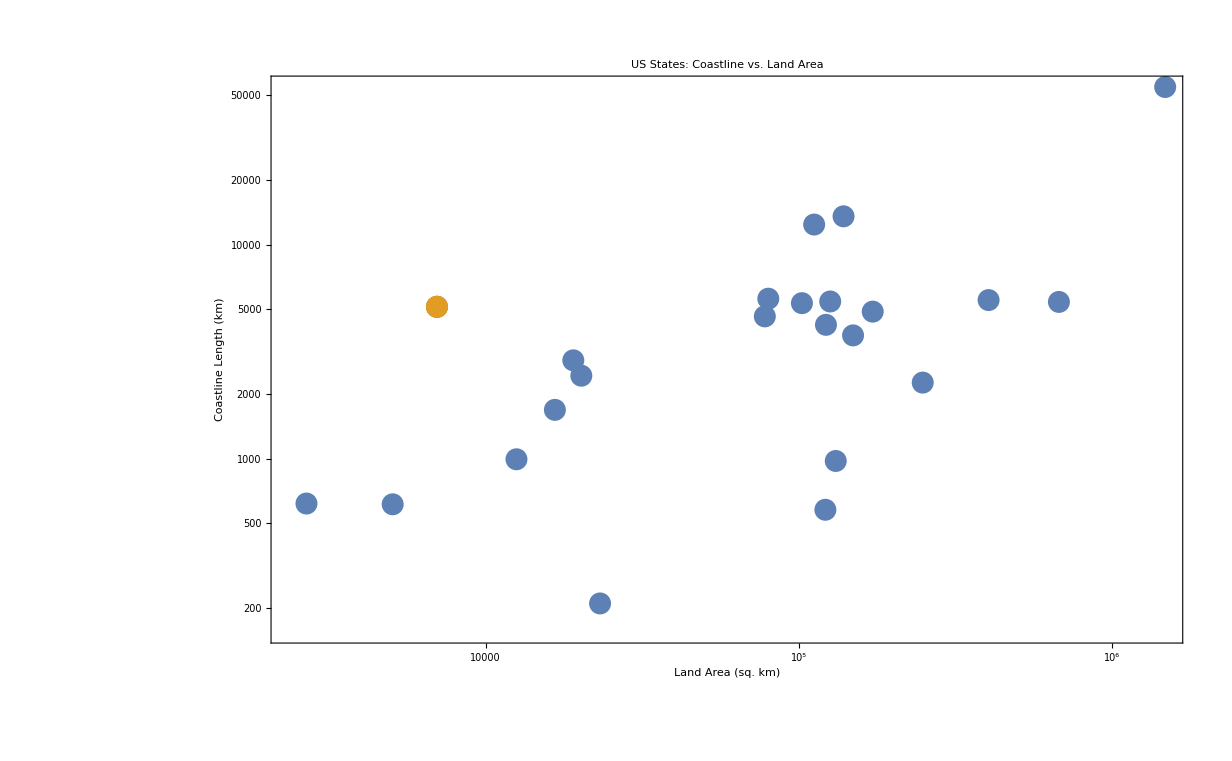

```mathematica
ListLogLogPlot[{graphArray,maryland},Axes->False,Frame->True,FrameLabel->{"Land Area (sq. km)", "Coastline Length (km)"}, PlotLabel->"US States: Coastline vs. Land Area", PlotRange->Full,BaseStyle->{FontFamily->"Helvetica Neue",FontSize->18}]
```